```mathematica
LommelR[m_,n_,x_]:=Pochhammer[n,m](x/2)^-m HypergeometricPFQ[{(1-m)/2,-m/2},{n,-m,1-n-m},-x^2];
```

```mathematica
Expand[LommelR[3,1/2,1/x]]
```

-6 x+15 x^3

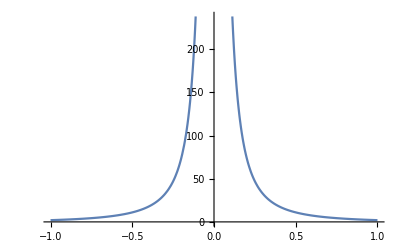

```mathematica
Plot[Out[17],{x,-1,1}]
```